```mathematica
datScEl=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/ScalarElectron.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
datScLe=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/ScalarLepton.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
datScMu=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/ScalarMuon.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
datScYu=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/ScalarYukawa.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
datVeEl=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/VectorElectron.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
datVeMu=Sort[DeleteCases[Import["/home/gerrit/Documents/Projects/MuonSpectrumMC/results/VectorMuon.csv","Data"],{_,999.|21.,_}|{_,_,999.|21.}],#1[[1]]<#2[[1]]&];
```

```mathematica
data=datScEl;
```

```mathematica
data90={data[[All,1]],data[[All,2]]}//Transpose;
data95={data[[All,1]],data[[All,3]]}//Transpose;
nlm90=NonlinearModelFit[data90//Log10,a+f*x*x+b*Exp[x*c],{a,b,c,f},x];
nlm95=NonlinearModelFit[data95//Log10,a+f*x*x+b*Exp[x*c],{a,b,c,f},x];
```

```mathematica
dataplot=Show[ListLogLogPlot[data90],ListLogLogPlot[data95]];
```

```mathematica
niceplot=Show[LogLogPlot[10^nlm90[Log10[x]],{x,First[data][[1]],Last[data][[1]]}],LogLogPlot[10^nlm95[Log10[x]],{x,First[data][[1]],Last[data][[1]]}]];
```

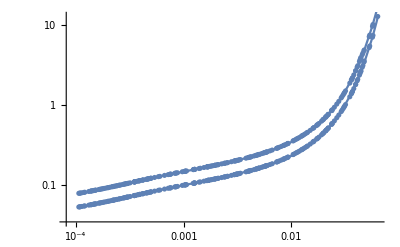

```mathematica
Show[dataplot,niceplot]
```